```mathematica
Quit[];
```

```mathematica
u[t_,x_]:=(1/2)*(1+Tanh[(1/4)*(x+((5*t)/2))]);
```

```mathematica
u[t,x]
```

1/2 (1+Tanh[1/4 ((5 t)/2+x)])

```mathematica
u1=D[u[t,x],t]
```

5/16 Sech[1/4 ((5 t)/2+x)]^2

```mathematica
u2=D[u[t,x],x]
```

1/8 Sech[1/4 ((5 t)/2+x)]^2

```mathematica
u3=D[D[u[t,x],x],x]
```

-1/16 Sech[1/4 ((5 t)/2+x)]^2 Tanh[1/4 ((5 t)/2+x)]

```mathematica
u1-u3-u[t,x]*u2-u[t,x]*(1-u[t,x])
```

5/16 Sech[1/4 ((5 t)/2+x)]^2+1/16 Sech[1/4 ((5 t)/2+x)]^2 Tanh[1/4 ((5 t)/2+x)]-1/16 Sech[1/4 ((5 t)/2+x)]^2 (1+Tanh[1/4 ((5 t)/2+x)])-1/2 (1+1/2 (-1-Tanh[1/4 ((5 t)/2+x)])) (1+Tanh[1/4 ((5 t)/2+x)])

```mathematica
Simplify[u1-u3-u[t,x]*u2-u[t,x]*(1-u[t,x])]
```

0

```mathematica
Quit[];
```

```mathematica
(*ξ=x-ct ->ODE c=-5/2 *)
```

```mathematica
u[ξ_]:=(1/2)*(1+Tanh[ξ/4]);
```

```mathematica
u[ξ]
```

1/2 (1+Tanh[ξ/4])

```mathematica
u[0]
```

1/2

```mathematica
u1=D[u[ξ],ξ]
```

1/8 Sech[ξ/4]^2

```mathematica
d1[ξ_]:=1/8 Sech[ξ/4]^2;(*1D*)
```

```mathematica
d1[0]
```

1/8

```mathematica
D[d1[ξ],ξ]
```

-1/16 Sech[ξ/4]^2 Tanh[ξ/4]

```mathematica
d2[ξ_]:=-1/16 Sech[ξ/4]^2 Tanh[ξ/4];(*2D*)
```

```mathematica
qq=(5/2)*d1[ξ]-d2[ξ]-u[ξ]*d1[ξ]-u[ξ]*(1-u[ξ])
```

5/16 Sech[ξ/4]^2+1/16 Sech[ξ/4]^2 Tanh[ξ/4]-1/16 Sech[ξ/4]^2 (1+Tanh[ξ/4])-1/2 (1+1/2 (-1-Tanh[ξ/4])) (1+Tanh[ξ/4])

```mathematica
Simplify[qq]
```

0

```mathematica
Quit[];
```

```mathematica
s=NDSolve[{X'[t] == Y[t],
Y'[t]==(5/2 )*Y[t]-X[t]*Y[t]-X[t]+((X[t])^2),X[0]==1/2,Y[0]==1/8},{X[t],Y[t]},{t,-8,8}]
```

{{X[t]→InterpolatingFunction[…][t],Y[t]→InterpolatingFunction[…][t]}}

```mathematica
Table[X[t]/.s,{t,-5,3}]
```

{{0.0758582},{0.119203},{0.182426},{0.268941},{0.377541},{0.5},{0.622459},{0.731058},{0.817574}}

```mathematica
Table[Y[t]/.s,{t,-5,3}]
```

{{0.0350519},{0.0524968},{0.0745732},{0.098306},{0.117502},{0.125},{0.117502},{0.0983058},{0.0745719}}

```mathematica
s=NDSolve[{X'[t] == Y[t],
Y'[t]==(5/2 )*Y[t]-X[t]*Y[t]-X[t]+((X[t])^2),X[0]==1/2,Y[0]==1/8},{X[t],Y[t]},{t,-8,8}]
```

{{X[t]→InterpolatingFunction[…][t],Y[t]→InterpolatingFunction[…][t]}}

```mathematica
Table[X[t]/.s,{t,-5,3}]
```

{{0.0758582},{0.119203},{0.182426},{0.268941},{0.377541},{0.5},{0.622459},{0.731058},{0.817574}}

```mathematica
Table[Y[t]/.s,{t,-5,3}]
```

{{0.0350519},{0.0524968},{0.0745732},{0.098306},{0.117502},{0.125},{0.117502},{0.0983058},{0.0745719}}

```mathematica
Quit[];
```

```mathematica
(*Case1*)
```

```mathematica
ss=DSolve[{X'[t] == Y[t],
Y'[t]==(5/2 )*Y[t],X[0]==1/2,Y[0]==1/8},{X[t],Y[t]},{t,-5,3}]
```

{{X[t]→1/20 (9+ⅇ^(5 t/2)),Y[t]→1/8 ⅇ^(5 t/2)}}

```mathematica
sol=Simplify[ExpToTrig[ss]]
```

{{X[t]→1/20 (9+Cosh[(5 t)/2]+Sinh[(5 t)/2]),Y[t]→1/8 (Cosh[(5 t)/2]+Sinh[(5 t)/2])}}

```mathematica
Plot[{Evaluate[X[t]/.sol],(1/2)*(1+Tanh[t/4])},{t,-5,3},PlotRange->All,PlotStyle->{{Red,Dashed,Thick},{Green,DotDashed,Thick}},PlotLabels->{"(ū)_1","u"},Frame->True]
```

-Graphics-

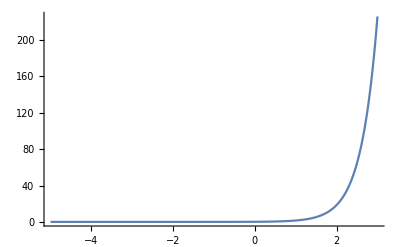

```mathematica
Plot[{Evaluate[Y[t]/.sol],1/8 Sech[ξ/4]^2},{t,-5,3},PlotRange->All]
```

```mathematica
(*Case2*)
```

```mathematica
Quit[];
```

```mathematica
ss=DSolve[{X'[t] == Y[t],
Y'[t]==-X[t],X[0]==1/2,Y[0]==1/8},{X[t],Y[t]},{t,-5,5}]
```

{{X[t]→1/8 (4 Cos[t]+Sin[t]),Y[t]→1/8 (Cos[t]-4 Sin[t])}}

```mathematica
sol=Simplify[ExpToTrig[ss]]
```

{{X[t]→1/8 (4 Cos[t]+Sin[t]),Y[t]→1/8 (Cos[t]-4 Sin[t])}}

```mathematica
Plot[{Evaluate[X[t]/.sol],(1/2)*(1+Tanh[t/4])},{t,-5,2},PlotRange->All,PlotStyle->{{Red,Dashed,Thick},{Green,DotDashed,Thick}},PlotLabels->{"(ū)_1","u"},Frame->True]
```

-Graphics-

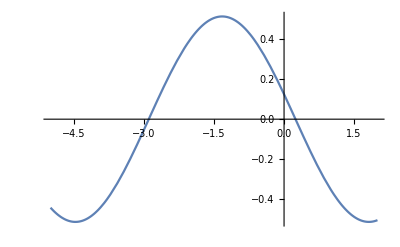

```mathematica
Plot[{Evaluate[Y[t]/.sol],1/8 Sech[ξ/4]^2},{t,-5,2},PlotRange->All]
```

```mathematica
(*Case3*)
```

```mathematica
Quit[];(*choose this case*)
```

```mathematica
ss=DSolve[{X'[t] == Y[t],
Y'[t]==(5/2 )*Y[t]-X[t],X[0]==1/2,Y[0]==1/8},{X[t],Y[t]},{t,-5,5}]
```

{{X[t]→-1/12 ⅇ^(t/2) (-7+ⅇ^(3 t/2)),Y[t]→(7 ⅇ^(t/2))/24-ⅇ^(2 t)/6}}

```mathematica
sol=Simplify[ExpToTrig[ss]]
```

{{X[t]→-1/12 (Cosh[t/2]+Sinh[t/2]) (-7+Cosh[(3 t)/2]+Sinh[(3 t)/2]),Y[t]→1/24 (7 Cosh[t/2]-4 Cosh[2 t]+7 Sinh[t/2]-4 Sinh[2 t])}}

```mathematica
Plot[{Evaluate[X[t]/.sol],(1/2)*(1+Tanh[t/4])},{t,-3,2},PlotRange->All,PlotStyle->{{Red,Dashed,Thick},{Black,DotDashed,Thick}},PlotLabels->{"(ū)_1","u"},Frame->True]
```

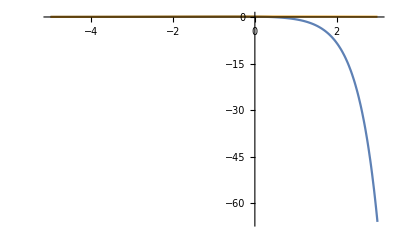

```mathematica
Plot[{Evaluate[Y[t]/.sol],1/8 Sech[t/4]^2},{t,-5,3},PlotRange->All]
```

```mathematica
Quit[];
```

```mathematica
u[t_,x_]:=(1/2)*(1+Tanh[(1/4)*(x+((5*t)/2))]);
```

```mathematica
Plot3D[u[t,x],{t,-1,1},{x,-8,8}]
```

-Graphics3D-